# Phase Transition for (SU(2))_R in Type-I 2HDM Model with LR Parity

## Basic Model Setting for the Higgs

This model is based on left-right parity with type-I 2HDM Higgs sector for each Higgs H_L and H_R. We made the following assumptions:

For each Higgs sector H_L and H_R, there are two Higgs doublet Φ_(1(L,R)) and Φ_(2(L,R)). The Higgs charge is H_L=(1,2,1,-1/2) and H_R=(1,1,2,1/2). Both doublets are charged under gauge groups.

For H_L or H_R, only the field Φ_(2(L,R)) couple with fermions via Yukawa interactions. Details for the Yukawa couplings are shown in the note “setup”.

Parity is imposed so that the dimensionless quartic couplings should be the same for H_L and H_R. This parity can be softly broken by the mass term of H_R.

The doublet Φ_(1L)is assumed to be much heavier than the electroweak scale so that at the EW scale, only the field Φ_(2L) plays an important role.

We assume negative coupling h_1, h_2, h_3 to achieve small effective quartic coupling λ_eff=λ_R+h_1+h_2+2 h_3. In the following mathematical expressions, we use positive value for the symbol h_i, with negative sign extracted out in the expressions of the potential.

## Tree Level

The tree level potential for the H_R is setted as:

```mathematica
$Assumptions={{ρ,α,θ,μR,κ,δ,λR,Subscript[h, 1],Subscript[h, 2],Subscript[h, 3],g,gy,ytp,x1r,x1i,y1r,y1i,x2r,x2i,y2r,y2i}∈PositiveReals,{λR-(Subscript[h, 1]+Subscript[h, 2]+2 Subscript[h, 3])}∈PositiveReals};
(*Global assumptions for the parameters*)
VR=Tr[-μR^2(Φ1†.Φ1 +Φ2†.Φ2)-κ ⅇ^(ⅈ δ)Φ1†.Φ2 - κ ⅇ^(-ⅈ δ)Φ2†.Φ1 + λR/2((Φ1†.Φ1)^2+(Φ2†.Φ2)^2)-Subscript[h, 1] (Φ1†.Φ2)(Φ2†.Φ1)-Subscript[h, 2](Φ1†.Φ1)(Φ2†.Φ2)-Subscript[h, 3]((Φ1†.Φ2)^2+(Φ2†.Φ1)^2)];
```

In the following calculations, we need to parameterize the Higgs doublet into fields. The field can be written in the form:

```mathematica
Φ1=1/(√2)({{ϕ1p}, {ϕ10}});
Φ2=1/(√2)({{ϕ2p}, {ϕ20}});
```

where the components can be parameterized in standard form. Here we still use the basis where the lower component gets the vev for both of the doublets. Further more, as in James Cline’s paper[Reference], we assume the vev for both of the doublets are equal. Thus the parametrization can be:

```mathematica
param={ϕ1p->x1r+ⅈ x1i,ϕ10->ρ+y1r+ⅈ y1i,ϕ2p->x2r+ⅈ x2i,ϕ20->ρ+y2r+ⅈ y2i};
Φ1/.param//MatrixForm
Φ2/.param//MatrixForm
```

((ⅈ x1i+x1r)/(√2)
(ⅈ y1i+y1r+ρ)/(√2))

((ⅈ x2i+x2r)/(√2)
(ⅈ y2i+y2r+ρ)/(√2))

Then we can have the parameterized potential:

```mathematica
Vpr=VR/.param//FullSimplify
```

1/8 (-4 μR^2 (x1i^2+x1r^2+x2i^2+x2r^2+y1i^2+y1r^2+y2i^2+y2r^2+2 y1r ρ+2 ρ (y2r+ρ))-4 ⅇ^(-ⅈ δ) κ ((x1i-ⅈ x1r) (x2i+ⅈ x2r)+(ⅈ y1i+y1r+ρ) (-ⅈ y2i+y2r+ρ))-4 ⅇ^(ⅈ δ) κ ((x1i+ⅈ x1r) (x2i-ⅈ x2r)+(-ⅈ y1i+y1r+ρ) (ⅈ y2i+y2r+ρ))+λR ((x1i^2+x1r^2+y1i^2+(y1r+ρ)^2)^2+(x2i^2+x2r^2+y2i^2+(y2r+ρ)^2)^2)-2 ((x1i-ⅈ x1r) (x2i+ⅈ x2r)+(ⅈ y1i+y1r+ρ) (-ⅈ y2i+y2r+ρ)) ((x1i+ⅈ x1r) (x2i-ⅈ x2r)+(-ⅈ y1i+y1r+ρ) (ⅈ y2i+y2r+ρ)) h_1-2 (x1i^2+x1r^2+y1i^2+(y1r+ρ)^2) (x2i^2+x2r^2+y2i^2+(y2r+ρ)^2) h_2-2 (((x1i-ⅈ x1r) (x2i+ⅈ x2r)+(ⅈ y1i+y1r+ρ) (-ⅈ y2i+y2r+ρ))^2+((x1i+ⅈ x1r) (x2i-ⅈ x2r)+(-ⅈ y1i+y1r+ρ) (ⅈ y2i+y2r+ρ))^2) h_3)

The tree-level potential for the field ρ is calculated by simply replace the other fields to 0. The result is:

```mathematica
truevac={x1r->0,x1i->0,y1r->0,y1i->0,x2r->0,x2i->0,y2r->0,y2i->0};
Vtree=Vpr/.truevac//FullSimplify
```

-1/4 ρ^2 (4 μR^2-λR ρ^2+4 κ Cos[δ]+ρ^2 (h_1+h_2+2 h_3))

## Mass-Spectrum

The mass spectrum for the particles should be calculated to finish the loop-corrections for the potential.

### Scalar sector

The scalar sector should be calculated by the derivative. We also need to set the phase δ=0 when we calculate the mass spectrum.

```mathematica
fields={x1r,x1i,y1r,y1i,x2r,x2i,y2r,y2i};
DVpr=D[Vpr/.{δ->0},{variables}];
DDVpr=D[DVpr,{variables}];
MassMatrix=DDVpr/.truevac//FullSimplify;
MassMatrix//MatrixForm
Mass=Eigenvalues[MassMatrix]//FullSimplify;
Mass//MatrixForm
```

(1/2 (-2 μR^2+λR ρ^2-ρ^2 h_2) | 0 | 0 | 0 | -κ-1/2 ρ^2 (h_1+2 h_3) | 0 | 0 | 0
0 | 1/2 (-2 μR^2+λR ρ^2-ρ^2 h_2) | 0 | 0 | 0 | -κ-1/2 ρ^2 (h_1+2 h_3) | 0 | 0
0 | 0 | 1/2 (-2 μR^2+3 λR ρ^2-ρ^2 (h_1+h_2+2 h_3)) | 0 | 0 | 0 | -κ-ρ^2 (h_1+h_2+2 h_3) | 0
0 | 0 | 0 | 1/2 (-2 μR^2+λR ρ^2-ρ^2 (h_1+h_2-2 h_3)) | 0 | 0 | 0 | -κ-2 ρ^2 h_3
-κ-1/2 ρ^2 (h_1+2 h_3) | 0 | 0 | 0 | 1/2 (-2 μR^2+λR ρ^2-ρ^2 h_2) | 0 | 0 | 0
0 | -κ-1/2 ρ^2 (h_1+2 h_3) | 0 | 0 | 0 | 1/2 (-2 μR^2+λR ρ^2-ρ^2 h_2) | 0 | 0
0 | 0 | -κ-ρ^2 (h_1+h_2+2 h_3) | 0 | 0 | 0 | 1/2 (-2 μR^2+3 λR ρ^2-ρ^2 (h_1+h_2+2 h_3)) | 0
0 | 0 | 0 | -κ-2 ρ^2 h_3 | 0 | 0 | 0 | 1/2 (-2 μR^2+λR ρ^2-ρ^2 (h_1+h_2-2 h_3)))

(1/2 (-2 (κ+μR^2)+3 λR ρ^2-3 ρ^2 (h_1+h_2+2 h_3))
1/2 (-2 (κ+μR^2)+λR ρ^2-ρ^2 (h_1+h_2+2 h_3))
1/2 (-2 (κ+μR^2)+λR ρ^2-ρ^2 (h_1+h_2+2 h_3))
1/2 (-2 (κ+μR^2)+λR ρ^2-ρ^2 (h_1+h_2+2 h_3))
1/2 (2 κ-2 μR^2+λR ρ^2+ρ^2 (h_1-h_2+2 h_3))
1/2 (2 κ-2 μR^2+λR ρ^2+ρ^2 (h_1-h_2+2 h_3))
κ-μR^2+(3 λR ρ^2)/2+1/2 ρ^2 (h_1+h_2+2 h_3)
κ-μR^2+(λR ρ^2)/2-1/2 ρ^2 (h_1+h_2-6 h_3))

This result is should be used when calculating the quantum corrections to the effective potential. To show the particle masses at the true vacuum, we need to replace the true vev into the expressions.

```mathematica
veveq=(D[Vtree/.{δ->0},ρ]==0)//FullSimplify;
vevcond=Solve[veveq,{μR}][[1]]
massvac=Mass/.vevcond//FullSimplify;
massvac//MatrixForm
```

{μR→-(√(-2 κ+λR ρ^2-ρ^2 h_1-ρ^2 h_2-2 ρ^2 h_3))/(√2)}

(ρ^2 (λR-h_1-h_2-2 h_3)
0
0
0
2 κ+ρ^2 (h_1+2 h_3)
2 κ+ρ^2 (h_1+2 h_3)
2 κ+λR ρ^2+ρ^2 (h_1+h_2+2 h_3)
2 (κ+2 ρ^2 h_3))

### Fermion and Gauge Bosons

The heaviest fermion is the new quark, whose mass square is given by:

```mathematica
mtpsq[ρ_]:=1/2 ytp^2 ρ^2;
```

The gauge boson mass square is given by:

```mathematica
mWRsq[ρ_]:=g^2/2 ρ^2;
mZRsq[ρ_]:=(g^2+gy^2)/2 ρ^2;
```

## Coleman-Weinberg Corrections

The Coleman-Weinberg corrections is given by:

V_CW=1/(64 π^2)[∑_scalars n_i(m_i(ρ))^4(log (m_i(ρ))^2/Λ^2-3/2)+∑_(gauge bosons) n_i(m_i(ρ))^4(log (m_i(ρ))^2/Λ^2-5/6)-∑_fermions n_i(m_i(ρ))^4(log (m_i(ρ))^2/Λ^2-3/2)]

```mathematica
VCW=1/(64 π^2)Sum[Mass[[i]]^2(Log[Abs[Mass[[i]]]/Λ^2]-3/2),{i,1,Length[Mass]}]+1/(64 π^2)(3 mZRsq[ρ]^2(Log[mZRsq[ρ]/Λ^2]-5/6))+1/(64 π^2)(6 mWRsq[ρ]^2(Log[mWRsq[ρ]/Λ^2]-5/6))-1/(64 π^2)(2 mtpsq[ρ]^2(Log[mtpsq[ρ]/Λ^2]-3/2))//Simplify
```

1/(256 π^2)(g^4 ρ^4 (-5+6 Log[(g^2 ρ^2)/(2 Λ^2)])+3 (g^2+gy^2)^2 ρ^4 (-5/6+Log[((g^2+gy^2) ρ^2)/(2 Λ^2)])-ytp^4 ρ^4 (-3+2 Log[(ytp^2 ρ^2)/(2 Λ^2)])+4 (-3/2+Log[Abs[κ-μR^2+(λR ρ^2)/2-1/2 ρ^2 (h_1+h_2-6 h_3)]/Λ^2]) (κ-μR^2+(λR ρ^2)/2-1/2 ρ^2 (h_1+h_2-6 h_3))^2+2 (-3/2+Log[Abs[2 κ-2 μR^2+λR ρ^2+ρ^2 (h_1-h_2+2 h_3)]/(2 Λ^2)]) (2 κ-2 μR^2+λR ρ^2+ρ^2 (h_1-h_2+2 h_3))^2+4 (-3/2+Log[Abs[κ-μR^2+(3 λR ρ^2)/2+1/2 ρ^2 (h_1+h_2+2 h_3)]/Λ^2]) (κ-μR^2+(3 λR ρ^2)/2+1/2 ρ^2 (h_1+h_2+2 h_3))^2+3 (-3/2+Log[Abs[2 (κ+μR^2)-λR ρ^2+ρ^2 (h_1+h_2+2 h_3)]/(2 Λ^2)]) (2 (κ+μR^2)-λR ρ^2+ρ^2 (h_1+h_2+2 h_3))^2+(-3/2+Log[Abs[2 (κ+μR^2)-3 λR ρ^2+3 ρ^2 (h_1+h_2+2 h_3)]/(2 Λ^2)]) (2 (κ+μR^2)-3 λR ρ^2+3 ρ^2 (h_1+h_2+2 h_3))^2)

## Finite-Temperature Correction

The finite-temperature correction are expressed as:

V_FT=T^4/(2 π^2)[∑J_B(m_i^2/T^2)-∑J_F(m_i^2/T^2)]

The function J_B and J_F can be expressed in expansion:

```mathematica
JB[x_]:=-π^4/45+π^2/12 x^2-π/6 x^3-1/32 x^4(Log[x^2]-5.4076);
JF[x_]:=-7 π^4/360-π^2/24 x^2-1/32 x^4(Log[x^2]-2.6351);
```

Then the correction can be calculated as:

```mathematica
VFT=T^4/(2 π^2)(Sum[JB[(√Abs[Mass[[i]]])/T],{i,1,Length[Mass]}]+6JB[(√mWRsq[ρ])/T]+3JB[(√mZRsq[ρ])/T]-2JF[(√mtpsq[ρ])/T])
```

1/(2 π^2)T^4 (-(8 π^4)/45+(π^2 Abs[κ-μR^2+(λR ρ^2)/2-1/2 ρ^2 (h_1+h_2-6 h_3)])/(12 T^2)-(π Abs[κ-μR^2+(λR ρ^2)/2-1/2 ρ^2 (h_1+h_2-6 h_3)]^(3/2))/(6 T^3)+(π^2 Abs[2 κ-2 μR^2+λR ρ^2+ρ^2 (h_1-h_2+2 h_3)])/(12 T^2)-(π Abs[2 κ-2 μR^2+λR ρ^2+ρ^2 (h_1-h_2+2 h_3)]^(3/2))/(6 √2 T^3)+(π^2 Abs[-2 (κ+μR^2)+3 λR ρ^2-3 ρ^2 (h_1+h_2+2 h_3)])/(24 T^2)-(π Abs[-2 (κ+μR^2)+3 λR ρ^2-3 ρ^2 (h_1+h_2+2 h_3)]^(3/2))/(12 √2 T^3)+(π^2 Abs[-2 (κ+μR^2)+λR ρ^2-ρ^2 (h_1+h_2+2 h_3)])/(8 T^2)-(π Abs[-2 (κ+μR^2)+λR ρ^2-ρ^2 (h_1+h_2+2 h_3)]^(3/2))/(4 √2 T^3)+(π^2 Abs[κ-μR^2+(3 λR ρ^2)/2+1/2 ρ^2 (h_1+h_2+2 h_3)])/(12 T^2)-(π Abs[κ-μR^2+(3 λR ρ^2)/2+1/2 ρ^2 (h_1+h_2+2 h_3)]^(3/2))/(6 T^3)+6 (-π^4/45+(g^2 π^2 ρ^2)/(24 T^2)-(π (g^2 ρ^2)^(3/2))/(12 √2 T^3)-(g^4 ρ^4 (-5.4076+Log[(g^2 ρ^2)/(2 T^2)]))/(128 T^4))+3 (-π^4/45+((g^2+gy^2) π^2 ρ^2)/(24 T^2)-(π ((g^2+gy^2) ρ^2)^(3/2))/(12 √2 T^3)-((g^2+gy^2)^2 ρ^4 (-5.4076+Log[((g^2+gy^2) ρ^2)/(2 T^2)]))/(128 T^4))-2 (-(7 π^4)/360-(π^2 ytp^2 ρ^2)/(48 T^2)-(ytp^4 ρ^4 (-2.6351+Log[(ytp^2 ρ^2)/(2 T^2)]))/(128 T^4))-(Abs[κ-μR^2+(λR ρ^2)/2-1/2 ρ^2 (h_1+h_2-6 h_3)]^2 (-5.4076+Log[Abs[κ-μR^2+(λR ρ^2)/2-1/2 ρ^2 (h_1+h_2-6 h_3)]/T^2]))/(32 T^4)-(Abs[2 κ-2 μR^2+λR ρ^2+ρ^2 (h_1-h_2+2 h_3)]^2 (-5.4076+Log[Abs[2 κ-2 μR^2+λR ρ^2+ρ^2 (h_1-h_2+2 h_3)]/(2 T^2)]))/(64 T^4)-(Abs[-2 (κ+μR^2)+3 λR ρ^2-3 ρ^2 (h_1+h_2+2 h_3)]^2 (-5.4076+Log[Abs[-2 (κ+μR^2)+3 λR ρ^2-3 ρ^2 (h_1+h_2+2 h_3)]/(2 T^2)]))/(128 T^4)-(3 Abs[-2 (κ+μR^2)+λR ρ^2-ρ^2 (h_1+h_2+2 h_3)]^2 (-5.4076+Log[Abs[-2 (κ+μR^2)+λR ρ^2-ρ^2 (h_1+h_2+2 h_3)]/(2 T^2)]))/(128 T^4)-(Abs[κ-μR^2+(3 λR ρ^2)/2+1/2 ρ^2 (h_1+h_2+2 h_3)]^2 (-5.4076+Log[Abs[κ-μR^2+(3 λR ρ^2)/2+1/2 ρ^2 (h_1+h_2+2 h_3)]/T^2]))/(32 T^4))

## Plots

Now we arrive the summary for the effective potential. Let’s make plots. First let’s sum over all the corrections:

```mathematica
Veff=Vtree+VCW+VFT
```

1/(2 π^2)T^4 (-(8 π^4)/45+(π^2 Abs[κ-μR^2+(λR ρ^2)/2-1/2 ρ^2 (h_1+h_2-6 h_3)])/(12 T^2)-(π Abs[κ-μR^2+(λR ρ^2)/2-1/2 ρ^2 (h_1+h_2-6 h_3)]^(3/2))/(6 T^3)+(π^2 Abs[2 κ-2 μR^2+λR ρ^2+ρ^2 (h_1-h_2+2 h_3)])/(12 T^2)-(π Abs[2 κ-2 μR^2+λR ρ^2+ρ^2 (h_1-h_2+2 h_3)]^(3/2))/(6 √2 T^3)+(π^2 Abs[-2 (κ+μR^2)+3 λR ρ^2-3 ρ^2 (h_1+h_2+2 h_3)])/(24 T^2)-(π Abs[-2 (κ+μR^2)+3 λR ρ^2-3 ρ^2 (h_1+h_2+2 h_3)]^(3/2))/(12 √2 T^3)+(π^2 Abs[-2 (κ+μR^2)+λR ρ^2-ρ^2 (h_1+h_2+2 h_3)])/(8 T^2)-(π Abs[-2 (κ+μR^2)+λR ρ^2-ρ^2 (h_1+h_2+2 h_3)]^(3/2))/(4 √2 T^3)+(π^2 Abs[κ-μR^2+(3 λR ρ^2)/2+1/2 ρ^2 (h_1+h_2+2 h_3)])/(12 T^2)-(π Abs[κ-μR^2+(3 λR ρ^2)/2+1/2 ρ^2 (h_1+h_2+2 h_3)]^(3/2))/(6 T^3)+6 (-π^4/45+(g^2 π^2 ρ^2)/(24 T^2)-(π (g^2 ρ^2)^(3/2))/(12 √2 T^3)-(g^4 ρ^4 (-5.4076+Log[(g^2 ρ^2)/(2 T^2)]))/(128 T^4))+3 (-π^4/45+((g^2+gy^2) π^2 ρ^2)/(24 T^2)-(π ((g^2+gy^2) ρ^2)^(3/2))/(12 √2 T^3)-((g^2+gy^2)^2 ρ^4 (-5.4076+Log[((g^2+gy^2) ρ^2)/(2 T^2)]))/(128 T^4))-2 (-(7 π^4)/360-(π^2 ytp^2 ρ^2)/(48 T^2)-(ytp^4 ρ^4 (-2.6351+Log[(ytp^2 ρ^2)/(2 T^2)]))/(128 T^4))-(Abs[κ-μR^2+(λR ρ^2)/2-1/2 ρ^2 (h_1+h_2-6 h_3)]^2 (-5.4076+Log[Abs[κ-μR^2+(λR ρ^2)/2-1/2 ρ^2 (h_1+h_2-6 h_3)]/T^2]))/(32 T^4)-(Abs[2 κ-2 μR^2+λR ρ^2+ρ^2 (h_1-h_2+2 h_3)]^2 (-5.4076+Log[Abs[2 κ-2 μR^2+λR ρ^2+ρ^2 (h_1-h_2+2 h_3)]/(2 T^2)]))/(64 T^4)-(Abs[-2 (κ+μR^2)+3 λR ρ^2-3 ρ^2 (h_1+h_2+2 h_3)]^2 (-5.4076+Log[Abs[-2 (κ+μR^2)+3 λR ρ^2-3 ρ^2 (h_1+h_2+2 h_3)]/(2 T^2)]))/(128 T^4)-(3 Abs[-2 (κ+μR^2)+λR ρ^2-ρ^2 (h_1+h_2+2 h_3)]^2 (-5.4076+Log[Abs[-2 (κ+μR^2)+λR ρ^2-ρ^2 (h_1+h_2+2 h_3)]/(2 T^2)]))/(128 T^4)-(Abs[κ-μR^2+(3 λR ρ^2)/2+1/2 ρ^2 (h_1+h_2+2 h_3)]^2 (-5.4076+Log[Abs[κ-μR^2+(3 λR ρ^2)/2+1/2 ρ^2 (h_1+h_2+2 h_3)]/T^2]))/(32 T^4))-1/4 ρ^2 (4 μR^2-λR ρ^2+4 κ Cos[δ]+ρ^2 (h_1+h_2+2 h_3))+1/(256 π^2)(g^4 ρ^4 (-5+6 Log[(g^2 ρ^2)/(2 Λ^2)])+3 (g^2+gy^2)^2 ρ^4 (-5/6+Log[((g^2+gy^2) ρ^2)/(2 Λ^2)])-ytp^4 ρ^4 (-3+2 Log[(ytp^2 ρ^2)/(2 Λ^2)])+4 (-3/2+Log[Abs[κ-μR^2+(λR ρ^2)/2-1/2 ρ^2 (h_1+h_2-6 h_3)]/Λ^2]) (κ-μR^2+(λR ρ^2)/2-1/2 ρ^2 (h_1+h_2-6 h_3))^2+2 (-3/2+Log[Abs[2 κ-2 μR^2+λR ρ^2+ρ^2 (h_1-h_2+2 h_3)]/(2 Λ^2)]) (2 κ-2 μR^2+λR ρ^2+ρ^2 (h_1-h_2+2 h_3))^2+4 (-3/2+Log[Abs[κ-μR^2+(3 λR ρ^2)/2+1/2 ρ^2 (h_1+h_2+2 h_3)]/Λ^2]) (κ-μR^2+(3 λR ρ^2)/2+1/2 ρ^2 (h_1+h_2+2 h_3))^2+3 (-3/2+Log[Abs[2 (κ+μR^2)-λR ρ^2+ρ^2 (h_1+h_2+2 h_3)]/(2 Λ^2)]) (2 (κ+μR^2)-λR ρ^2+ρ^2 (h_1+h_2+2 h_3))^2+(-3/2+Log[Abs[2 (κ+μR^2)-3 λR ρ^2+3 ρ^2 (h_1+h_2+2 h_3)]/(2 Λ^2)]) (2 (κ+μR^2)-3 λR ρ^2+3 ρ^2 (h_1+h_2+2 h_3))^2)

The next step is plug in the parameter. For the parity, we need the gauge coupling for the (SU(2))_R is the same for the (SU(2))_L. Further more, as discussed above, the quartic coupling λ_R should be the same as λ_SM. The Yukawa coupling for the new quark should be the same for the top quark.
In addition, we ask that the effective quartic coupling λ_eff=λ_R-(h_1+h_2+2 h_3) to be positive, but try to be as small as possible to get strong first order phase transition. The mass parameter μ_R as well as κ can be different from the SM and be regarded as free parameters.
The plots are made here. First, the tree-level potential and the tree-level plus CW correction is plotted out. These result should be close to each other. Then we plotted out the finite temperature effective potential at different temperature to find the first order phase transition. In general, the potential should be dependent on the CP-violating phase δ. This parameter, however, only appears in the tree-level potential. To show the phase transition properties, we here simply ask it to be zero. We will take it back when goes into the baryon asymmetry calculation when needed.

```mathematica
SMparam={g->0.65,gy->0.36,λR->0.13,ytp->0.9};
newparam={μR->1,κ->5,Subscript[h, 1]->0.02,Subscript[h, 2]->0.02,Subscript[h, 3]->0.02};
scale={Λ->7,T->7};
```

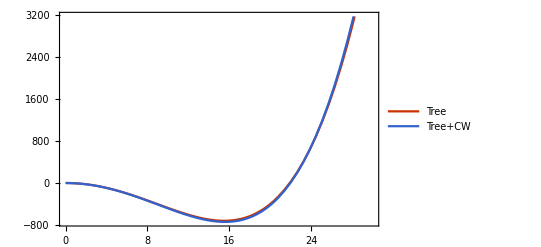

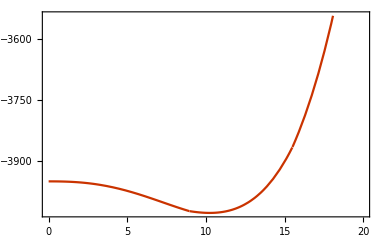

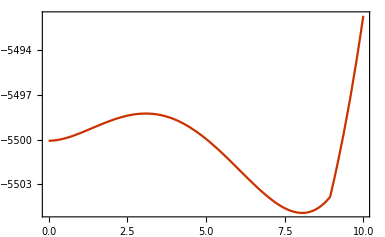

```mathematica
Vtreeparam=Vtree/.SMparam/.newparam/.scale/.{δ->0};
VCWparam=VCW/.SMparam/.newparam/.scale/.{δ->0};
Veffparam=Veff/.SMparam/.newparam/.scale/.{δ->0};
Plot[{Vtreeparam,Vtreeparam+VCWparam},{ρ,0,30},PlotLegends->{"Tree","Tree+CW"}]
Plot[Veffparam,{ρ,0,20}]
Plot[Veff/.SMparam/.newparam/.{Λ->7.6,T->7.6}/.{δ->0},{ρ,0,10}]
```

From the previous plots, we can clearly see that this model can give a first order phase transition. Further more, the CW correction is very small, so that we can almost neglect it.

## Approximated analysis

Now we need to focus on how to express the formula analytically. Otherwise we cannot list out the condition for strong first order phase transition. The general form of the effective potential can be written as:

V_eff=λ_eff/4 ρ^4-E T ρ^3+D (T-T_0)ρ^2

The Higgs quartic couplings are very small compare to the gauge coupling, thus we only include the gauge couplings in the coefficient E. Now we have:

E=3 g_R^3/(16 π)

The condition for strong 1st order phase transition is given by:

(2E)/λ_eff=(3 g_R^3)/(8π(λ_R-h_1-h_2-2 h_3))>1

In this condition, the parameter g_R=0.65 and λ_R=0.13 is fixed.
To check whether this approximation is reasonable, we should compare the effective potential with only tree-level plus the FT contributed from fermions and gauge bosons. This potential is:

```mathematica
VFTapp=T^4/(2 π^2)(6JB[(√mWRsq[ρ])/T]+3JB[(√mZRsq[ρ])/T]-2JF[(√mtpsq[ρ])/T]);
Vapp=Vtreeparam+(VFTapp/.SMparam/.newparam/.scale/.{δ->0})//Simplify
```

-1908.92-0.894506 ρ^2-0.188964 ρ^3+0.0170734 ρ^4-0.00053295 ρ^4 Log[ρ]

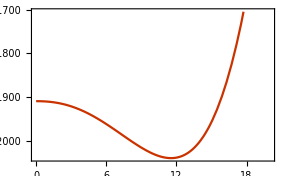

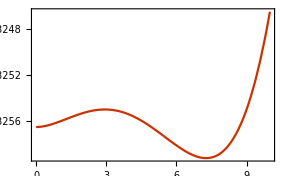

```mathematica
Plot[Vapp,{ρ,0,20}]
Plot[Vtreeparam+VFTapp/.SMparam/.newparam/.{Λ->8,T->8}/.{δ->0},{ρ,0,10}]
```

## References

J. M. Cline, K. Kainulainen, A. P. Vischer, Dynamics of two-Higgs-doublet CP violation and baryogenesis at the electroweak phase transition, Phys. Rev. D. 54(1996) 2451-2472. doi: 10.1103/physrrevd.54-2451. arXiv: hep-ph/9506284